```mathematica
fs=10;
n=1;f=List[];nmax=200;T=500;W=10;
r1=0.5;r2=2.0;
While[n≤nmax,l=List[];
t=1;
k=W;
While[t<T,AppendTo[l,k];
a=RandomInteger[{1,2}];
k=If[a==1,(k*r2),(k*r1)];
t++;];
AppendTo[f,l];
n++;];
(*p1=ListLinePlot[f,ScalingFunctions->"Log",PlotTheme->"Scientific",PlotStyle->Directive[Thin],FrameLabel->{"Time","Capital"}];*)
```

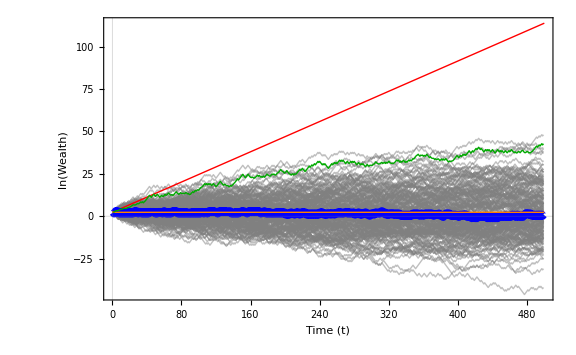

```mathematica
p1=ListLinePlot[Log[f],PlotTheme->"Scientific",PlotStyle->Directive[Opacity[0.5],Gray,Thin],PlotRange->{Automatic,{-200,200}},FrameLabel->{"Time (t)","ln(Wealth)"},PlotLegends->Placed[LineLegend[{Directive[Gray]},{"Individual Wealth"}],{Left,Top}],LabelStyle->Directive[FontFamily->"Calibri",Black,FontSize->fs]];
p2=ListLinePlot[Table[Log[W],T],PlotStyle->Directive[Black,Thick]];
p3=ListLinePlot[Log[Median[f]],PlotStyle->Directive[Blue,Thickness[0.01]],PlotLegends->Placed[LineLegend[{Directive[Blue]},{"Median Wealth"}],{Left,Top}],LabelStyle->Directive[FontFamily->"Calibri",Black,FontSize->fs]];
p4=ListLinePlot[Log[Mean[f]],PlotStyle->Directive[Darker[Green],Thick],PlotLegends->Placed[LineLegend[{Directive[Darker[Green]]},{"Mean Wealth"}],{Left,Top}],LabelStyle->Directive[FontFamily->"Calibri",Black,FontSize->fs]];
v=Plot[Log[W]+Log[Sqrt[r2*r1]]*x,{x,0,T},PlotStyle->Directive[Orange,Thick],PlotLegends->Placed[LineLegend[{Directive[Orange]},{"Time Growth Average: \!\(\*SubscriptBox[\(g\), \(t\)]\)"}],{Left,Top}],LabelStyle->Directive[FontFamily->"Calibri",Black,FontSize->fs]];
expect=Plot[Log[W*(1/2*r2+1/2*r1)^x],{x,0,T},PlotStyle->Directive[Red,Thick],PlotLegends->Placed[LineLegend[{Directive[Red]},{"Expected Wealth"}],{Left,Top}],LabelStyle->Directive[FontFamily->"Calibri",Black,FontSize->fs]];
Wmin=Min[Log[f][[;;,-1]],Log[W]+Log[Sqrt[r2*r1]]*T,Log[W]+Log[(1/2*r2+1/2*r1)]*T];
Wmax=Max[Log[f][[;;,-1]],Log[W]+Log[Sqrt[r2*r1]]*T,Log[W]+Log[(1/2*r2+1/2*r1)]*T];
multibet=Show[p1,expect,p3,v,p4, PlotRange-> Full,ImageSize->Large]
(*multibet=Show[p1,expect,p4,v(*,v,expect,p3*)(*(*p2,*)p3,p4,v,*)]*)
(*oneovertitwealth=1/Total[f[[;;,#]]]&[Range[1,Length[f[[1]]]]];
ListPlot[ReverseSort[oneovertitwealth[[100]]*f[[;;,100]]],PlotRange->Full]*)
```

```mathematica
exportloc="/Users/bertverbruggen/Library/CloudStorage/OneDrive-VrijeUniversiteitBrussel/Documenten/Documents/Onderzoek/IntegratedIntelligence/RL_Experiment/Paper2023/paper/Data/Data_Analysis/";Export[exportloc<>"multibettest.pdf",multibet]
```

/Users/bertverbruggen/Library/CloudStorage/OneDrive-VrijeUniversiteitBrussel/Documenten/Documents/Onderzoek/IntegratedIntelligence/RL_Experiment/Paper2023/paper/Data/Data_Analysis/multibettest.pdf